# Ballistic Transmission Coefficients, 21 dec 07

Implementations for some of methods discussed in the review by J-S Wang, J Wang, and J-T Lu, ``Quantum thermal transport in nanostructure".

## Input

The force parameters are in the following format:
k_11^L | k_01^L | 0 | 0 | 0 | 0 | 0
k_10^L | k_11^L | k_01^L | 0 | 0 | 0 | 0
0 | k_10^L | k_00^L | V^LC | 0 | 0 | 0
0 | 0 | V^CL | K^C | V^CR | 0 | 0
0 | 0 | 0 | V^RC | k_00^R | k_01^R | 0
0 | 0 | 0 | 0 | k_10^R | k_11^R | k_01^R
0 | 0 | 0 | 0 | 0 | k_10^R | k_11^R,
extending in the L and R directions indefinitely.  Only these submatrices highlighted in red need to be entered explicitly.

```mathematica
kL11={{4.502, -1.591},{-1.591, 2.252}};
kL00=kL11;
kL01={{0.0, 0.0},{-1.591, 0.0}};
VLC={{0.0, 0.0},{-1.837, 0.0}};
KC={{6.0, -1.643},{-1.643, 1.8}};
VRC={{0.0,-1.423}};
kR00={{4.501}};
kR11=kR00;
kR01={{-2.250}};
```

## Eigenvalue problems

Here we give the subroutines for the dispersion relation calculation (of the leads) and the generalized eigenvalue problem, where λ = e^(i2πk/N)=e^(i q a.) eigen[ ] returns the frequencies and associated polarization vectors.  The generalizedeigen[ ] returns {Ε^+, Λ_(+,)Ε^-,Λ_-}. + means |λ| < 1.+

```mathematica
eigen[{k11_,k01_}, λ_]:= Module[{d,Ω2,Ε},
d = k11 + (1/λ)*Transpose[k01] + λ * k01;
{Ω2,Ε}=Eigensystem[d];
{Sqrt[Ω2], Ε}
]
```

```mathematica
generalizedeigen[{k11_,k01_},ω_]:=Module[ {m,iden,A,B,t,b,Λplist, Λmlist, Ep, Em,Λp,Λm,λ, v,vec,j},
m=Length[k11];
iden = IdentityMatrix[m];
A=Table[0.0, {2*m},{2*m}];
t = Range[1,m];
b = Range[m+1,2m];
A[[t,t]]=ω^2*iden -k11;
A[[t,b]]= -iden;
A[[b,t]]=Transpose[k01];
B=Table[0.0, {2*m},{2*m}];
B[[t,t]]=k01;
B[[b,b]]= iden;
{λ,vec}=Eigensystem[{A,B}];
Λplist={};
Λmlist={};
Ep={};
Em={};
For[j=1,j≤2m,++j,
If[Abs[λ[[j]]] < 1.0,
AppendTo[Λplist, λ[[j]]];
v = vec[[j,t]];
v=v/Sqrt[Conjugate[v].v];
AppendTo[Ep, v],
If[Abs[λ[[j]]] > 1.0,
If[Abs[λ[[j]]]>10^9, λ[[j]]=10^9];
AppendTo[Λmlist, λ[[j]]];
v = vec[[j,t]];
v=v/Sqrt[Conjugate[v].v];
AppendTo[Em,v]
];
]
];
Ep = Transpose[Ep];
Em = Transpose[Em];
Λp = DiagonalMatrix[Λplist];
Λm = DiagonalMatrix[Λmlist];
{Ep, Λp, Em, Λm}
]
```

## Surface Green's function

We have three different algorithms, (1) simple iteration, (2) accelerated iteration, (3) generalized eigenvalue problem.  The input ω should be complex with a small imaginary part, i.e., ω → ω + i η.  Define ϵ to be the convergence factor for algorithms (1) and (2).

```mathematica
ϵ = 0.00001;
surface1green[{k00_, k11_, k01_}, ω_]:=Module[{m,Ω2,k10,g,gn},
m=Length[k00];
Ω2=ω^2*IdentityMatrix[m];
k10=Transpose[k01];
g=Table[0.0, {m},{m}];
gn = Inverse[Ω2 -k11];
While[ (Max @@ Abs[gn-g]) > ϵ,
g = gn;
gn = Inverse[Ω2 - k11 - k01.g.k10];
];
Inverse[Ω2 - k00 - k01.gn.k10]
]

surface2green[{k00_,k11_,k01_}, ω_]:= Module[{Ω2,s,e,α,β,g},
Ω2=ω^2*IdentityMatrix[Length[k00]];
s=k00;
e=k11;
α=k01;
While[ (Max @@ Abs[α]) > ϵ,
g=Inverse[Ω2 -e];
β = Transpose[α];
s = s + α.g.β;
e = e + α.g.β + β.g.α;
α = α.g.α
];
Inverse[Ω2-s]
]

surface3green[{k00_,k11_,k01_}, ω_]:= Module[{ Ω2,ep,Λp,em,Λm,F },
Ω2=ω^2*IdentityMatrix[Length[k00]];
{ep,Λp,em,Λm}= generalizedeigen[{k11,k01}, ω];
F = ep.Λp.PseudoInverse[ep];
Inverse[Ω2 - k00 - k01.F]
]
```

The three functions defined above work only for the right lead; for the left lead, we transform the force constants so that it looks like a right lead, and call the right-lead routines.  The result is then transformed back.   The parameter of the function leftlead[ ] is the name of routine applied (without any argument).

```mathematica
leftlead[sgf_Symbol, ω_]:=Module[{k00p,k11p,k01p,g},
k00p=flip[kL00];
k11p=flip[kL11];
k01p=Transpose[flip[kL01]];
g=sgf[{k00p,k11p,k01p}, ω];
flip[g]
]

flip[m_]:=Module[{n,mp,i,j},
n=Length[m];
mp=Table[0,{n},{n}];
For[i=1,i≤n,++i,
For[j=1,j≤n,++j,
mp[[i,j]]=m[[n-i+1,n-j+1]]
]
];
mp
]
```

## Caroli formula

Compute the transmission according to the Caroli formula, T[ω]=Tr(G^r Γ_L G^a Γ_R).

```mathematica
caroli[ω_]:=Module[{gR,gL,ΣR,ΣL,m,Ω2,Gr,ΓR,ΓL,Tw},
gR = surface2green[{kR00,kR11,kR01}, ω];
gL=leftlead[surface2green, ω];
ΣR = Transpose[VRC].gR.VRC;
ΣL=Transpose[VLC].gL.VLC;
m=Length[KC];
Ω2=ω^2*IdentityMatrix[m];
Gr=Inverse[Ω2-KC-ΣR-ΣL];
ΓR=-2.0*Im[ΣR];
ΓL=-2.0*Im[ΣL];
Tw=Tr[Gr.ΓL.ConjugateTranspose[Gr].ΓR];
Re[Tw]
]
```

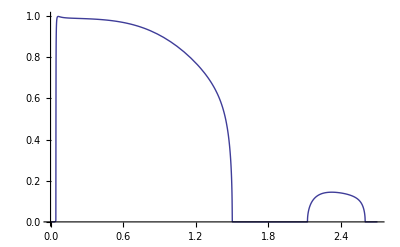

```mathematica
Plot[caroli[w+ 0.00001*I],{w, 0.00001, 2.7}]
```

## Mode-matching

Here we solve the mode-matching linear equations:
[-k_10^LF_L^-(-1)+(ω^2-k_00^L)]u_0-V^LC u^C=k_10^L(F_L^+(-1)-F_L^-(-1)) u_0^+,
-V^CL u_0+(ω^2-K^C)u^C-V^CR u_(N+1)=0,
-V^RC u^C+[(ω^2-k_00^R)-k_01^R F_R^+(+1)] u_(N+1)=0.
Force constants are passed globally. mode pick a particular column in E = (ϵ_1,ϵ_2, ...) matrix. Note that one must add iη to the real frequency.  In order to have the diagonal pseudoinverse work, η need sufficiently small.  The transmission amplitude t_n'n^RL as a vector index by n' is computed.  The function returns the partial transmission T_n'n[ω] = v_n'^R|t_n'n^RL|^2/v_n^L.

```mathematica
modematch[ω_Complex,mode_Integer]:=Module[{mL,mR,n,ntot,A,l,c,r,epL,ΛpL,emL,ΛmL,u0p,FpL,FmL,epR,ΛpR,emR,ΛmR,epRinv,F1R,b,uNp1,(* tRLnn *),vR,vL},
mL = Length[kL00];
mR=Length[kR00];
n = Length[KC];
ntot = mL + n + mR;
A = Table[0.0, {ntot},{ntot}];
l = Range[1,mL];
c=Range[mL+1,mL+n];
r=Range[mL+n+1,mL+n+mR];
A[[l,l]]=ω^2*IdentityMatrix[mL]-kL00;
A[[l,c]]=-VLC;
A[[c,l]]=-Transpose[VLC];
A[[c,c]]=ω^2*IdentityMatrix[n]-KC;
A[[c,r]]=-Transpose[VRC];
A[[r,c]]=-VRC;
A[[r,r]]=ω^2*IdentityMatrix[mR]-kR00;
{epL,ΛpL,emL,ΛmL}= generalizedeigen[{kL11,kL01}, ω];
(* take the first column of ep1, note the difference between ell, l, and one, 1 *)
u0p=epL[[l,mode]];
FpL =epL.diagpsinv[ΛpL].PseudoInverse[epL];
FmL=emL.diagpsinv[ΛmL].PseudoInverse[emL];
{epR,ΛpR,emR,ΛmR}= generalizedeigen[{kR11,kR01}, ω];
epRinv = PseudoInverse[epR];
F1R=epR.ΛpR.epRinv;
A[[l,l]]+=-Transpose[kL01].FmL;
A[[r,r]]+= -kR01.F1R;
b = Table[0.0, {ntot}];
b[[l]]=Transpose[kL01].(FpL-FmL).u0p;
uNp1=LinearSolve[A,b];
tRLnn=epRinv.uNp1[[r]];
(* compute group velocity matrix, in units of lattice spacings *)
vR=Chop[velocity[epR,ΛpR,kR01]/(-2.0*Re[ω]*I)];
vL=Chop[velocity[epL,ΛpL,kL01]/(-2.0*Re[ω]*I)];
vR.Abs[tRLnn]^2*(diagpsinv[vL])[[mode,mode]]
]

(* Take a pseudoinverse of diagonal matrix *)
diagpsinv[mat_]:=Module[{i,len,matinv},
len = Length[mat];
matinv=Table[0.0, {len},{len}];
For[i=1, i≤len,++i,
If[Abs[mat[[i,i]]]>10^-5, matinv[[i,i]]=1.0/mat[[i,i]]]
];
matinv
]

(* compute velocity matrix f *)
velocity[e_, Λ_, k01_]:=Module[{et,f},
et = ConjugateTranspose[e];
f=et.k01.e.Λ - Conjugate[Λ].et.Transpose[k01].e
]
```

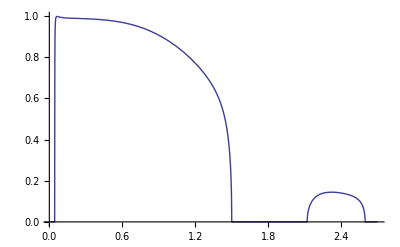

```mathematica
Plot[modematch[w+0.0000001*I,1][[1]], {w, 0.01, 2.7}]
```

## Piccard formula

to be rewitten

## Fisher - Lee relation

They are given by G_(N+1,0)=g_(R,00)^r V^RC G^r V^CL g_(L,00)^r and  t_n'n^RL=i 2(ω [(E_R^+)^-1(G_(N+1,0)((E_L^-)^T))^-1 ])_n'n v_n^L.

```mathematica
fisherlee[ω_,mode_Integer,modep_Integer]:=Module[{gR,gL,ΣR,ΣL,m,Ω2,Gr,ERinv,ELinv, epR,ΛpR,emR,ΛmR,epL,ΛpL,emL,ΛmL,vL, prod,Gnp1},
(* compute g^r and G^r first as in caroli[] *)
gR = surface2green[{kR00,kR11,kR01}, ω];
gL=leftlead[surface2green, ω];
ΣR = Transpose[VRC].gR.VRC;
ΣL=Transpose[VLC].gL.VLC;
m=Length[KC];
Ω2=ω^2*IdentityMatrix[m];
Gr=Inverse[Ω2-KC-ΣR-ΣL];
Gnp1=gR.VRC.Gr.Transpose[VLC].gL;
(* pseudo-inverse of Subscript[E, R]^+ and (Subscript[E, L]^-)^T *)
{epR,ΛpR,emR,ΛmR}= generalizedeigen[{kR11,kR01}, ω];
ERinv = PseudoInverse[epR];
{epL,ΛpL,emL,ΛmL}= generalizedeigen[{kL11,kL01}, ω];
ELinv = PseudoInverse[Transpose[emL]];
(* reduced group velocity (v/a) of left lead *)
vL=Chop[velocity[epL,ΛpL,kL01]/(-2.0*Re[ω]*I)];
prod = ERinv . Gnp1. ELinv;
(* for reasons I don't understand, we should multiply by -1, not I, here in front of 2ω??   May be related to the fact that E can be multiplied by an arbitrary phase. *)
tRLnnfisher = -(2.0*ω)*prod[[modep, mode]]*vL[[mode,mode]]
]
```